## Summary

This week, I’ve been building the c++ code for de2dgammadgamma. The notebook has one more section to convert the functions to CForm.

## Numerical derivatives

```mathematica
Import["/home/chengling/Research/Project/Cell/AnalyticalG/cellGPU/analysescript/test_N1000_p3.80000_T0.00010000_et0.000000.nc","Datasets"]
```

{/BoxMatrix,/additionalData,/postion,/time,/type,/velocity}

```mathematica
test=Import["/home/chengling/Research/Project/Cell/AnalyticalG/cellGPU/analysescript/test_N1000_p3.80000_T0.00010000_et0.000000.nc","Data"];
```

```mathematica
test[[3]][[1]]
```

NumericArray[…]

```mathematica
getData[fname_]:=Module[{t,n,frames,types,times,positions,posSet},
t=Import[fname,"Data"];
n=Length[t[[3,1]]]/2;
frames=Length[t[[3]]];
times=Flatten[t[[3]]];
types=t[[5,1]];
positions={};
Do[
posSet=t[[3,fr]];
AppendTo[positions,Table[{posSet[[2*i+1]],posSet[[2*i+2]]},{i,0,n-1}]];
,{fr,1,frames}];
{n,frames,positions,types,times}];
```

```mathematica
temp=getData["/home/chengling/Research/Project/Cell/AnalyticalG/cellGPU/analysescript/test_N1000_p3.80000_T0.00010000_et0.000000.nc"];
p=temp[[3,Length[temp[[3]]]]];
min=Min[p]-.1;max=Max[p]+.1;
vm=VoronoiMesh[p,{{min,max},{min,max}}];
VareasI=PropertyValue[{vm,2},MeshCellMeasure];
VperisI=RegionMeasure/@(MeshPrimitives[vm,2]/.Polygon[{x_,y__}]:>Line[{x,y,x}]);
```

```mathematica
polygons=MeshPrimitives[vm,2];
```

```mathematica
polygons[[534]][[1]]
```

{{15.9837,15.6624},{16.3615,16.2789},{15.8164,16.8101},{15.5883,16.7997},{15.1944,16.108},{15.575,15.6704}}

```mathematica
(*Pick the cell 534 to do numerical testing*)
```

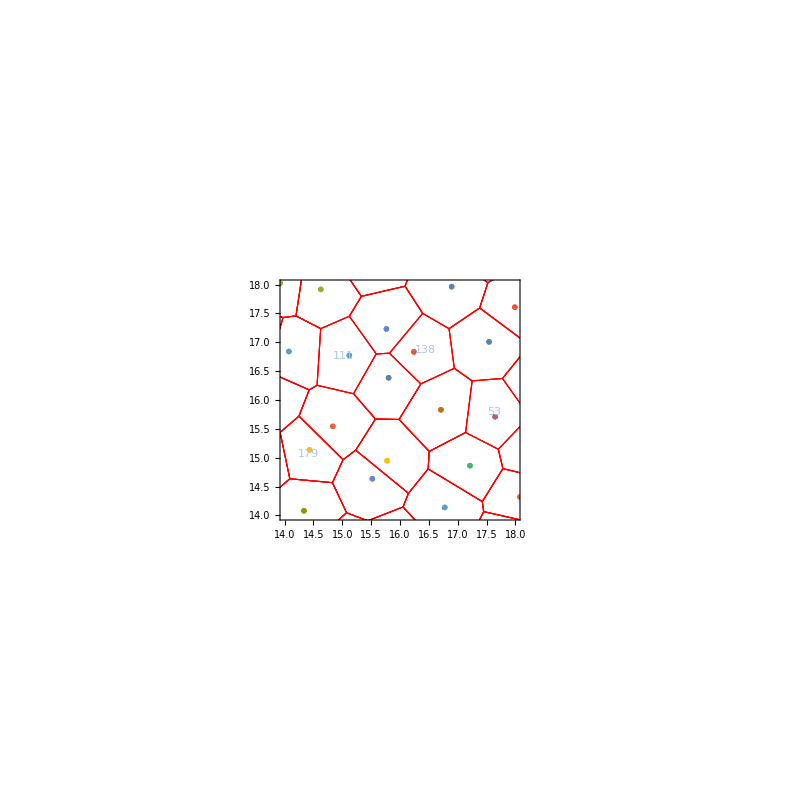

```mathematica
dl=ListPlot[Table[{p[[i]]},{i,1,Length[p]}],PlotMarkers->Table[i,{i,1,Length[p]}]];
Show[HighlightMesh[vm,{Style[2,White],Style[1,Thick,Red],Labeled[2,"Index"]}],dl,PlotRange->{{14,18},{14,18}},Frame->True]
```

```mathematica
polygon=Polygon[polygons[[534]][[1]]];
polygons[[534]][[1]]
```

{{15.9837,15.6624},{16.3615,16.2789},{15.8164,16.8101},{15.5883,16.7997},{15.1944,16.108},{15.575,15.6704}}

```mathematica
strainfor={{1,0.001},{0,1}};
strainback={{1,-0.001},{0,1}};
```

```mathematica
strainfor.#&/@polygons[[534]][[1]]
```

{{15.9994,15.6624},{16.3778,16.2789},{15.8332,16.8101},{15.6051,16.7997},{15.2105,16.108},{15.5907,15.6704}}

```mathematica
(*This is system sheard by dgamma=0.001*)
```

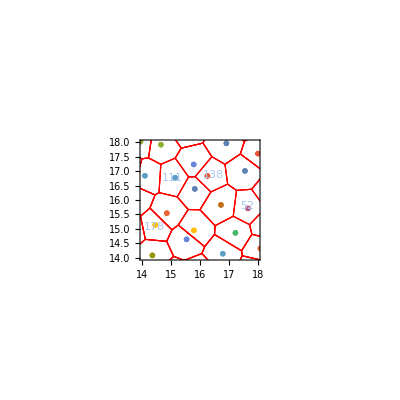

```mathematica
p0=strainfor.#&/@p;
vm0=VoronoiMesh[p0,{{min+0.001*min,max+0.001*max},{min,max}}];
dl0=ListPlot[Table[{p0[[i]]},{i,1,Length[p]}],PlotMarkers->Table[i,{i,1,Length[p]}]];
Show[HighlightMesh[vm0,{Style[2,White],Style[1,Thick,Red],Labeled[2,"Index"]}],dl0,PlotRange->{{14,18},{14,18}},Frame->True]
```

```mathematica
(*This is system sheard by dgamma=-0.001*)
```

```mathematica
Vareas0=PropertyValue[{vm0,2},MeshCellMeasure];
Vperis0=RegionMeasure/@(MeshPrimitives[vm0,2]/.Polygon[{x_,y__}]:>Line[{x,y,x}]);
```

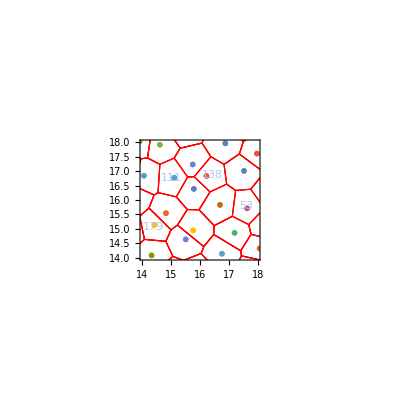

```mathematica
p1=strainback.#&/@p;
vm1=VoronoiMesh[p1,{{min+0.001*min,max+0.001*max},{min,max}}];
dl1=ListPlot[Table[{p1[[i]]},{i,1,Length[p]}],PlotMarkers->Table[i,{i,1,Length[p]}]];
Show[HighlightMesh[vm1,{Style[2,White],Style[1,Thick,Red],Labeled[2,"Index"]}],dl1,PlotRange->{{14,18},{14,18}},Frame->True]
```

```mathematica
Vareas1=PropertyValue[{vm1,2},MeshCellMeasure];
Vperis1=RegionMeasure/@(MeshPrimitives[vm1,2]/.Polygon[{x_,y__}]:>Line[{x,y,x}]);
```

```mathematica
(*This gives the numerical derivative of d2e/dgdg*)
((Vareas0[[533]]-1)^2+(Vperis0[[533]]-4)^2+(Vareas1[[534]]-1)^2+(Vperis1[[534]]-4)^2-2*((VareasI[[534]]-1)^2+(VperisI[[534]]-4)^2))/0.001/0.001
```

-1.54469

```mathematica
(*neighbor list for the cell 534*)
neighborlist={548,816,521,792,382,349};
```

```mathematica
Vareas=AnnotationValue[{vm,2},MeshCellMeasure];
Vperis=RegionMeasure/@(MeshPrimitives[vm,2]/.Polygon[{x_,y__}]:>Line[{x,y,x}]);
Vneighs=Length@@@cells;
```

```mathematica
Cross2d[r1_,r2_]:=r1[[1]]r2[[2]]-r1[[2]]r2[[1]]
voro[ri_,rj_,rk_]:=Module[{rij,rjk,rik,cross,d,α,β,γ},
rij=ri-rj;
rjk=rj-rk;
rik=ri-rk;

cross=Cross2d[rij,rjk];
d=2*cross*cross;

α=(rjk.rjk)*(rij.rik)/d;
β=-(rik.rik)*(rij.rjk)/d;
γ=(rij.rij)*(rik.rjk)/d;

α*ri+β*rj+γ*rk
];
```

```mathematica
ri={rix,riy}
rj={rjx,rjy}
rk={rkx,rky}
```

{rix,riy}

{rjx,rjy}

{rkx,rky}

```mathematica
hijk=voro[ri,rj,rk];
den=(rjx*rky-rjy*rkx)^3;
```

```mathematica
(*Analytical dirivatives of dhdr and dhdr*)
```

```mathematica
v1dri[r1_,r2_,r3_]:=(({{D[hijk[[1]],rix], D[hijk[[1]],riy]}, {D[hijk[[2]],rix], D[hijk[[2]],riy]}}))/.{rix->r1[[1]],riy->r1[[2]],rjx->r2[[1]],rjy->r2[[2]],rkx->r3[[1]],rky->r3[[2]]}
```

```mathematica
v2drirj[r1_,r2_,r3_]:={{{D[D[hijk[[1]],rix],rjx],D[D[hijk[[2]],rix],rjx]},
{D[D[hijk[[1]],riy],rjx],D[D[hijk[[2]],riy],rjx]}},
{{D[D[hijk[[1]],rix],rjy],D[D[hijk[[2]],rix],rjy]},
{D[D[hijk[[1]],riy],rjy],D[D[hijk[[2]],riy],rjy]}}}/.{rix->r1[[1]],riy->r1[[2]],rjx->r2[[1]],rjy->r2[[2]],rkx->r3[[1]],rky->r3[[2]]};
```

```mathematica
v2driri[r1_,r2_,r3_]:={{{D[D[hijk[[1]],rix],rix],D[D[hijk[[2]],rix],rix]},
{D[D[hijk[[1]],riy],rix],D[D[hijk[[2]],riy],rix]}},
{{D[D[hijk[[1]],rix],riy],D[D[hijk[[2]],rix],riy]},
{D[D[hijk[[1]],riy],riy],D[D[hijk[[2]],riy],riy]}}}/.{rix->r1[[1]],riy->r1[[2]],rjx->r2[[1]],rjy->r2[[2]],rkx->r3[[1]],rky->r3[[2]]};
```

```mathematica
(*Analytical dirivatives of dhdg and d2hdgdg*)
```

```mathematica
dridg={riy,0};
drjdg={rjy,0};
drkdg={rky,0};
(*dh2dgdg[r1_,r2_,r3_]:=(v2drirj[r1,r2,r3].{r2[[2]],0}).{r1[[2]],0}+(v2drirj[r1,r3,r2].{r3[[2]],0}).{r1[[2]],0}+(v2driri[r1,r2,r3].{r1[[2]],0}).{r1[[2]],0}+(v2drirj[r2,r1,r3].{r1[[2]],0}).{r2[[2]],0}+(v2drirj[r2,r3,r1].{r3[[2]],0}).{r2[[2]],0}+(v2driri[r2,r1,r3].{r2[[2]],0}).{r2[[2]],0}+(v2drirj[r3,r1,r2].{r1[[2]],0}).{r3[[2]],0}+(v2drirj[r3,r2,r1].{r2[[2]],0}).{r3[[2]],0}+(v2driri[r3,r1,r2].{r3[[2]],0}).{r3[[2]],0};*)
dh2dgdg[r1_,r2_,r3_]:={(v2drirj[r1,r2,r3][[1,1,1]]r2[[2]])r1[[2]]+(v2drirj[r1,r3,r2][[1,1,1]]r3[[2]])r1[[2]]+(v2driri[r1,r2,r3][[1,1,1]]r1[[2]])r1[[2]]+(v2drirj[r2,r1,r3][[1,1,1]]r1[[2]])r2[[2]]+(v2drirj[r2,r3,r1][[1,1,1]]r3[[2]])r2[[2]]+(v2driri[r2,r1,r3][[1,1,1]]r2[[2]])r2[[2]]+(v2drirj[r3,r1,r2][[1,1,1]]r1[[2]])r3[[2]]+(v2drirj[r3,r2,r1][[1,1,1]]r2[[2]])r3[[2]]+(v2driri[r3,r1,r2][[1,1,1]]r3[[2]])r3[[2]],(v2drirj[r1,r2,r3][[1,1,2]]r2[[2]])r1[[2]]+(v2drirj[r1,r3,r2][[1,1,2]]r3[[2]])r1[[2]]+(v2driri[r1,r2,r3][[1,1,2]]r1[[2]])r1[[2]]+(v2drirj[r2,r1,r3][[1,1,2]]r1[[2]])r2[[2]]+(v2drirj[r2,r3,r1][[1,1,2]]r3[[2]])r2[[2]]+(v2driri[r2,r1,r3][[1,1,2]]r2[[2]])r2[[2]]+(v2drirj[r3,r1,r2][[1,1,2]]r1[[2]])r3[[2]]+(v2drirj[r3,r2,r1][[1,1,2]]r2[[2]])r3[[2]]+(v2driri[r3,r1,r2][[1,1,2]]r3[[2]])r3[[2]]};
```

```mathematica
dhdg[r1_,r2_,r3_]:=(v1dri[r1,r2,r3].{r1[[2]],0})+(v1dri[r2,r1,r3].{r2[[2]],0})+(v1dri[r3,r1,r2].{r3[[2]],0});
```

```mathematica
originalh=voro[p[[816]],p[[521]],p[[466]]]
dh2dgdg[p[[816]],p[[521]],p[[466]]]
dhdg[p[[816]],p[[521]],p[[466]]]
```

Part::partd: Part specification p⟦816⟧ is longer than depth of object.

Part::partd: Part specification p⟦521⟧ is longer than depth of object.

Part::partd: Part specification p⟦466⟧ is longer than depth of object.

General::stop: Further output of Part::partd will be suppressed during this calculation.

((-p⟦466⟧+p⟦816⟧).(-p⟦466⟧+p⟦521⟧) (-p⟦521⟧+p⟦816⟧).(-p⟦521⟧+p⟦816⟧) p⟦466⟧)/(2 (-p⟦521⟧^2+p⟦466⟧ p⟦816⟧)^2)-((-p⟦466⟧+p⟦816⟧).(-p⟦466⟧+p⟦816⟧) (-p⟦521⟧+p⟦816⟧).(-p⟦466⟧+p⟦521⟧) p⟦521⟧)/(2 (-p⟦521⟧^2+p⟦466⟧ p⟦816⟧)^2)+((-p⟦466⟧+p⟦521⟧).(-p⟦466⟧+p⟦521⟧) (-p⟦521⟧+p⟦816⟧).(-p⟦466⟧+p⟦816⟧) p⟦816⟧)/(2 (-p⟦521⟧^2+p⟦466⟧ p⟦816⟧)^2)

Part::partd: Part specification p⟦816⟧ is longer than depth of object.

Part::partd: Part specification p⟦521⟧ is longer than depth of object.

Part::partd: Part specification p⟦466⟧ is longer than depth of object.

General::stop: Further output of Part::partd will be suppressed during this calculation.

Power::infy: Infinite expression 1/0^2 encountered.

Infinity::indet: Indeterminate expression 0 p ComplexInfinity encountered.

Power::infy: Infinite expression 1/0^2 encountered.

General::stop: Further output of Power::infy will be suppressed during this calculation.

Infinity::indet: Indeterminate expression 0 p ComplexInfinity encountered.

General::stop: Further output of Infinity::indet will be suppressed during this calculation.

{Indeterminate,Indeterminate}

Part::partd: Part specification p⟦816⟧ is longer than depth of object.

Part::partd: Part specification p⟦521⟧ is longer than depth of object.

Part::partd: Part specification p⟦466⟧ is longer than depth of object.

General::stop: Further output of Part::partd will be suppressed during this calculation.

Power::infy: Infinite expression 1/0^2 encountered.

Infinity::indet: Indeterminate expression 0 p ComplexInfinity encountered.

Power::infy: Infinite expression 1/0^2 encountered.

Infinity::indet: Indeterminate expression 0 p ComplexInfinity encountered.

Power::infy: Infinite expression 1/0^2 encountered.

General::stop: Further output of Power::infy will be suppressed during this calculation.

Infinity::indet: Indeterminate expression 0 p ComplexInfinity encountered.

General::stop: Further output of Infinity::indet will be suppressed during this calculation.

{Indeterminate,Indeterminate}

```mathematica
v2drirj[p[[792]],p[[466]],p[[521]]]
```

v2drirk[{15.7644,17.232},{16.2407,16.8343},{15.8032,16.3853}]

{{{0.0773484,0.0586187},{-0.481907,-0.618014}},{{0.444112,-0.563314},{1.09184,-0.00413408}}}

```mathematica
strainfor={{1,0.001},{0,1}};
strainback={{1,-0.001},{0,1}};
```

```mathematica
(*This verifies dhdg and dh2dgdg*)
hForward=voro[strainfor.p[[816]],strainfor.p[[521]],strainfor.p[[466]]]
hback=voro[strainback.p[[816]],strainback.p[[521]],strainback.p[[466]]]
(hback+hForward-2*originalh)/0.001^2
-(hback-hForward)/0.002
```

{16.3777,16.279}

{16.3453,16.2789}

{0.385362,0.433415}

{16.2053,0.0545846}

```mathematica
Total[{16.20533371806765,0.05458459342477795}]
```

16.2599

```mathematica
Simplify[({{{a111,a121},{a211,a221}},{{a112,a122},{a212,a222}}}.{xx,yy}).{xxx,yyy}]
```

{a111 xx xxx+a121 xxx yy+a211 xx yyy+a221 yy yyy,a112 xx xxx+a122 xxx yy+a212 xx yyy+a222 yy yyy}

```mathematica
Simplify[(Transpose[{{{a111,a121},{a211,a221}},{{a112,a122},{a212,a222}}}].{xx,yy}).{xxx,yyy}]
```

{a111 xx xxx+a121 xxx yy+a112 xx yyy+a122 yy yyy,a211 xx xxx+a221 xxx yy+a212 xx yyy+a222 yy yyy}

```mathematica
Simplify[(Transpose[{{{a111,a121},{a211,a221}},{{a112,a122},{a212,a222}}}].{xxx,yyy}).{xx,yy}]
```

{a111 xx xxx+a112 xxx yy+a121 xx yyy+a122 yy yyy,a211 xx xxx+a212 xxx yy+a221 xx yyy+a222 yy yyy}

```mathematica
Simplify[({{{a111,a121},{a211,a221}},{{a112,a122},{a212,a222}}}.{xx,yy})]
```

{{a111 xx+a121 yy,a211 xx+a221 yy},{a112 xx+a122 yy,a212 xx+a222 yy}}

```mathematica
Transpose[{{{a111,a121},{a211,a221}},{{a112,a122},{a212,a222}}}][[2,1,1]]//MatrixForm
```

```mathematica
Transpose[{{a11,a12},{a21,a22}}].{b1,b2}.{c1,c2}
{{a11,a12},{a21,a22}}.{c1,c2}.{b1,b2}
```

(a11 b1+a21 b2) c1+(a12 b1+a22 b2) c2

```mathematica
RotateLeft[{1,2,3,4},1]
```

{2,3,4,1}

```mathematica
(*dedh,de2dhdh*)
perimetii[hc_,hm_]:=Sqrt[(hc-hm).(hc-hm)];
areaiWithri[hc_,hm_,ri_]:=0.5*Cross2d[hm-ri,hc-ri];
eWithri[{h1_,h2_,h3_,h4_,h5_},ri_]:=(areaiWithri[h1,h5,ri]+areaiWithri[h2,h1,ri]+areaiWithri[h3,h2,ri]+areaiWithri[h4,h3,ri]+areaiWithri[h5,h4,ri]-1)^2+(perimetii[h1,h2]+perimetii[h2,h3]+perimetii[h3,h4]+perimetii[h4,h5]+perimetii[h5,h1]-4)^2
```

```mathematica
areai[hc_,hm_]:=0.5*Cross2d[hm,hc];
e[{h1_,h2_,h3_,h4_,h5_,h6_}]:=(areai[h1,h6]+areai[h2,h1]+areai[h3,h2]+areai[h4,h3]+areai[h5,h4]+areai[h6,h5]-1)^2+(perimetii[h1,h2]+perimetii[h2,h3]+perimetii[h3,h4]+perimetii[h4,h5]+perimetii[h5,h6]+perimetii[h6,h1]-4)^2
```

```mathematica
Cross2d[polygons[[138]][[1]][[5]],polygons[[138]][[1]][[1]]]
```

-5.00948

```mathematica
p[[521]]
```

{16.2407,16.8343}

```mathematica
e[polygons[[534]][[1]]]
eWithri[polygons[[138]][[1]],p[[521]]]
```

0.2756

0.255696

```mathematica
0.6809844951448113
```

0.680984

```mathematica
polygon=Polygon[polygons[[534]][[1]]];
Vareas=Area[polygon];
Vperis=Perimeter[polygon];
(Vperis-4)^2+(Vareas-1)^2
```

0.2756

```mathematica
h1={h1x,h1y};h2={h2x,h2y};h3={h3x,h3y};h4={h4x,h4y};h5={h5x,h5y};h6={h6x,h6y};
Simplify[D[D[e[{h1,h2,h3,h4,h5,h6}],h1x],h1x]]
```

2 ((0.5 h2y-0.5 h6y)^2+(perimetii^({0,0},{1,0})[{h6x,h6y},{h1x,h1y}]+perimetii^({1,0},{0,0})[{h1x,h1y},{h2x,h2y}])^2+(-4+perimetii[{h1x,h1y},{h2x,h2y}]+perimetii[{h2x,h2y},{h3x,h3y}]+perimetii[{h3x,h3y},{h4x,h4y}]+perimetii[{h4x,h4y},{h5x,h5y}]+perimetii[{h5x,h5y},{h6x,h6y}]+perimetii[{h6x,h6y},{h1x,h1y}]) (perimetii^({0,0},{2,0})[{h6x,h6y},{h1x,h1y}]+perimetii^({2,0},{0,0})[{h1x,h1y},{h2x,h2y}]))

```mathematica
(*Analytical derivatives of dedh and d2edhdh*)
```

```mathematica
ei123456=e[{h1,h2,h3,h4,h5,h6}];
dedh1[{h1_,h2_,h3_,h4_,h5_,h6_}]:={D[ei123456,h1x],D[ei123456,h1y]}/.{h1x->h1[[1]],h1y->h1[[2]],h2x->h2[[1]],h2y->h2[[2]],h3x->h3[[1]],h3y->h3[[2]],h4x->h4[[1]],h4y->h4[[2]],h5x->h5[[1]],h5y->h5[[2]],h6x->h6[[1]],h6y->h6[[2]]};
e2dh1h1[{h1_,h2_,h3_,h4_,h5_,h6_}]:={{D[D[ei123456,h1x],h1x],D[D[ei123456,h1x],h1y]},
{D[D[ei123456,h1x],h1y],D[D[ei123456,h1y],h1y]}}/.{h1x->h1[[1]],h1y->h1[[2]],h2x->h2[[1]],h2y->h2[[2]],h3x->h3[[1]],h3y->h3[[2]],h4x->h4[[1]],h4y->h4[[2]],h5x->h5[[1]],h5y->h5[[2]],h6x->h6[[1]],h6y->h6[[2]]};
e2dh1h2[{h1_,h2_,h3_,h4_,h5_,h6_}]:={{D[D[ei123456,h1x],h2x],D[D[ei123456,h1x],h2y]},
{D[D[ei123456,h1y],h2x],D[D[ei123456,h1y],h2y]}}/.{h1x->h1[[1]],h1y->h1[[2]],h2x->h2[[1]],h2y->h2[[2]],h3x->h3[[1]],h3y->h3[[2]],h4x->h4[[1]],h4y->h4[[2]],h5x->h5[[1]],h5y->h5[[2]],h6x->h6[[1]],h6y->h6[[2]]};
e2dh1h6[{h1_,h2_,h3_,h4_,h5_,h6_}]:={{D[D[ei123456,h1x],h6x],D[D[ei123456,h1x],h6y]},
{D[D[ei123456,h1y],h6x],D[D[ei123456,h1y],h6y]}}/.{h1x->h1[[1]],h1y->h1[[2]],h2x->h2[[1]],h2y->h2[[2]],h3x->h3[[1]],h3y->h3[[2]],h4x->h4[[1]],h4y->h4[[2]],h5x->h5[[1]],h5y->h5[[2]],h6x->h6[[1]],h6y->h6[[2]]};
e2dh1h3[{h1_,h2_,h3_,h4_,h5_,h6_}]:={{D[D[ei123456,h1x],h3x],D[D[ei123456,h1x],h3y]},
{D[D[ei123456,h1y],h3x],D[D[ei123456,h1y],h3y]}}/.{h1x->h1[[1]],h1y->h1[[2]],h2x->h2[[1]],h2y->h2[[2]],h3x->h3[[1]],h3y->h3[[2]],h4x->h4[[1]],h4y->h4[[2]],h5x->h5[[1]],h5y->h5[[2]],h6x->h6[[1]],h6y->h6[[2]]};
e2dh1h4[{h1_,h2_,h3_,h4_,h5_,h6_}]:={{D[D[ei123456,h1x],h4x],D[D[ei123456,h1x],h4y]},
{D[D[ei123456,h1y],h4x],D[D[ei123456,h1y],h4y]}}/.{h1x->h1[[1]],h1y->h1[[2]],h2x->h2[[1]],h2y->h2[[2]],h3x->h3[[1]],h3y->h3[[2]],h4x->h4[[1]],h4y->h4[[2]],h5x->h5[[1]],h5y->h5[[2]],h6x->h6[[1]],h6y->h6[[2]]};
e2dh1h5[{h1_,h2_,h3_,h4_,h5_,h6_}]:={{D[D[ei123456,h1x],h5x],D[D[ei123456,h1x],h5y]},
{D[D[ei123456,h1y],h5x],D[D[ei123456,h1y],h5y]}}/.{h1x->h1[[1]],h1y->h1[[2]],h2x->h2[[1]],h2y->h2[[2]],h3x->h3[[1]],h3y->h3[[2]],h4x->h4[[1]],h4y->h4[[2]],h5x->h5[[1]],h5y->h5[[2]],h6x->h6[[1]],h6y->h6[[2]]};
```

Part::partd: Part specification h6⟦1⟧ is longer than depth of object.

Part::partd: Part specification h1⟦2⟧ is longer than depth of object.

Part::partd: Part specification h6⟦2⟧ is longer than depth of object.

General::stop: Further output of Part::partd will be suppressed during this calculation.

```mathematica
(*This is to numerically test dedh and d2edrdr*)
```

```mathematica
e1x[vetice_,alpha_,dx_]:=Module[{p2,poly2},
p2=polygons[[vetice]][[1]];
p2[[alpha]]+={dx,0};
poly2=Polygon[p2];
Vareas=Area[poly2];
Vperis=Perimeter[poly2];
v0=(Vperis-4)^2+(Vareas-1)^2;
p2=polygons[[vetice]][[1]];
p2[[alpha]]+={-dx,0};
poly2=Polygon[p2];
Vareas=Area[poly2];
Vperis=Perimeter[poly2];
v1=(Vperis-4)^2+(Vareas-1)^2;
(v0-v1)/2/dx
]
e1y[vetice_,alpha_,dx_]:=Module[{p2,poly2},
p2=polygons[[vetice]][[1]];
p2[[alpha]]+={0,dx};
poly2=Polygon[p2];
Vareas=Area[poly2];
Vperis=Perimeter[poly2];
v0=(Vperis-4)^2+(Vareas-1)^2;
p2=polygons[[vetice]][[1]];
p2[[alpha]]+={0,-dx};
poly2=Polygon[p2];
Vareas=Area[poly2];
Vperis=Perimeter[poly2];
v1=(Vperis-4)^2+(Vareas-1)^2;
(v0-v1)/2/dx
]
e22xx[vetice_,alpha_,beta_,dx_]:=Module[{p2,poly2},
p2=polygons[[vetice]][[1]];
p2[[alpha]]+={dx,0};
p2[[beta]]+={dx,0};
poly2=Polygon[p2];
Vareas=Area[poly2];
Vperis=Perimeter[poly2];
v11=(Vperis-4)^2+(Vareas-1)^2;

p2=polygons[[vetice]][[1]];
p2[[alpha]]+={dx,0};
p2[[beta]]+={-dx,0};
poly2=Polygon[p2];
Vareas=Area[poly2];
Vperis=Perimeter[poly2];
v10=(Vperis-4)^2+(Vareas-1)^2;

p2=polygons[[vetice]][[1]];
p2[[alpha]]+={-dx,0};
p2[[beta]]+={dx,0};
poly2=Polygon[p2];
Vareas=Area[poly2];
Vperis=Perimeter[poly2];
v01=(Vperis-4)^2+(Vareas-1)^2;

p2=polygons[[vetice]][[1]];
p2[[alpha]]+={-dx,0};
p2[[beta]]+={-dx,0};
poly2=Polygon[p2];
Vareas=Area[poly2];
Vperis=Perimeter[poly2];
v00=(Vperis-4)^2+(Vareas-1)^2;

(v11+v00-v01-v10)/(4 dx^2)
]
e22yy[vetice_,alpha_,beta_,dx_]:=Module[{p2,poly2},
p2=polygons[[vetice]][[1]];
p2[[alpha]]+={0,dx};
p2[[beta]]+={0,dx};
poly2=Polygon[p2];
Vareas=Area[poly2];
Vperis=Perimeter[poly2];
v11=(Vperis-4)^2+(Vareas-1)^2;

p2=polygons[[vetice]][[1]];
p2[[alpha]]+={0,dx};
p2[[beta]]+={0,-dx};
poly2=Polygon[p2];
Vareas=Area[poly2];
Vperis=Perimeter[poly2];
v10=(Vperis-4)^2+(Vareas-1)^2;

p2=polygons[[vetice]][[1]];
p2[[alpha]]+={0,-dx};
p2[[beta]]+={0,dx};
poly2=Polygon[p2];
Vareas=Area[poly2];
Vperis=Perimeter[poly2];
v01=(Vperis-4)^2+(Vareas-1)^2;

p2=polygons[[vetice]][[1]];
p2[[alpha]]+={0,-dx};
p2[[beta]]+={0,-dx};
poly2=Polygon[p2];
Vareas=Area[poly2];
Vperis=Perimeter[poly2];
v00=(Vperis-4)^2+(Vareas-1)^2;

(v11+v00-v01-v10)/(4 dx^2)
]
e22xy[vetice_,alpha_,beta_,dx_]:=Module[{p2,poly2},
p2=polygons[[vetice]][[1]];
p2[[alpha]]+={dx,0};
p2[[beta]]+={0,dx};
poly2=Polygon[p2];
Vareas=Area[poly2];
Vperis=Perimeter[poly2];
v11=(Vperis-4)^2+(Vareas-1)^2;

p2=polygons[[vetice]][[1]];
p2[[alpha]]+={dx,0};
p2[[beta]]+={0,-dx};
poly2=Polygon[p2];
Vareas=Area[poly2];
Vperis=Perimeter[poly2];
v10=(Vperis-4)^2+(Vareas-1)^2;

p2=polygons[[vetice]][[1]];
p2[[alpha]]+={-dx,0};
p2[[beta]]+={0,dx};
poly2=Polygon[p2];
Vareas=Area[poly2];
Vperis=Perimeter[poly2];
v01=(Vperis-4)^2+(Vareas-1)^2;

p2=polygons[[vetice]][[1]];
p2[[alpha]]+={-dx,0};
p2[[beta]]+={0,-dx};
poly2=Polygon[p2];
Vareas=Area[poly2];
Vperis=Perimeter[poly2];
v00=(Vperis-4)^2+(Vareas-1)^2;

(v11+v00-v01-v10)/(4 dx^2)
]
e22yx[vetice_,alpha_,beta_,dx_]:=Module[{p2,poly2},
p2=polygons[[vetice]][[1]];
p2[[alpha]]+={0,dx};
p2[[beta]]+={dx,0};
poly2=Polygon[p2];
Vareas=Area[poly2];
Vperis=Perimeter[poly2];
v11=(Vperis-4)^2+(Vareas-1)^2;

p2=polygons[[vetice]][[1]];
p2[[alpha]]+={0,dx};
p2[[beta]]+={-dx,0};
poly2=Polygon[p2];
Vareas=Area[poly2];
Vperis=Perimeter[poly2];
v10=(Vperis-4)^2+(Vareas-1)^2;

p2=polygons[[vetice]][[1]];
p2[[alpha]]+={0,-dx};
p2[[beta]]+={dx,0};
poly2=Polygon[p2];
Vareas=Area[poly2];
Vperis=Perimeter[poly2];
v01=(Vperis-4)^2+(Vareas-1)^2;

p2=polygons[[vetice]][[1]];
p2[[alpha]]+={0,-dx};
p2[[beta]]+={-dx,0};
poly2=Polygon[p2];
Vareas=Area[poly2];
Vperis=Perimeter[poly2];
v00=(Vperis-4)^2+(Vareas-1)^2;

(v11+v00-v01-v10)/(4 dx^2)
]
```

```mathematica
a=1;
ddx=10^-5.;
cellindex=534;
{e1x[cellindex,a,ddx],e1y[cellindex,a,ddx]}
dedh1[polygons[[534]][[1]]]
```

{-0.572003,0.996053}

{-0.572003,0.996053}

```mathematica
a=1;
b=1;
ddx=10^-5.;
cellindex=534;
({{e22xx[cellindex,a,b,ddx], e22xy[cellindex,a,b,ddx]}, {e22yx[cellindex,a,b,ddx], e22yy[cellindex,a,b,ddx]}})//MatrixForm
```

(-0.370969 | -0.501238
-0.501238 | -1.00698)

```mathematica
(*Now we verify the analytical expression for de2dhdh*)
```

```mathematica
e2dh1h1[polygons[[534]][[1]]]//MatrixForm
```

(-0.370958 | -0.501238
-0.501238 | -1.00699)

```mathematica
e2dh1h3[RotateLeft[polygons[[534]][[1]],0]]//MatrixForm
```

(0.428396 | 0.945265
-0.698082 | -1.60151)

```mathematica
a=1;
b=2;
ddx=10^-5.;
cellindex=534;
({{e22xx[cellindex,a,b,ddx], e22xy[cellindex,a,b,ddx]}, {e22yx[cellindex,a,b,ddx], e22yy[cellindex,a,b,ddx]}})//MatrixForm
e2dh1h2[polygons[[534]][[1]]]//MatrixForm
```

(2.54278 | -0.571918
-3.08061 | 0.0436101)

(2.54278 | -0.571891
-3.08062 | 0.0436102)

```mathematica
a=1;
b=3;
ddx=10^-5.;
cellindex=534;
({{e22xx[cellindex,a,b,ddx], e22xy[cellindex,a,b,ddx]}, {e22yx[cellindex,a,b,ddx], e22yy[cellindex,a,b,ddx]}})//MatrixForm
e2dh1h3[polygons[[534]][[1]]]//MatrixForm
```

(0.428396 | 0.945265
-0.698082 | -1.60151)

(0.428396 | 0.945265
-0.698082 | -1.60151)

```mathematica
a=1;
b=4;
ddx=10^-5.;
cellindex=534;
({{e22xx[cellindex,a,b,ddx], e22xy[cellindex,a,b,ddx]}, {e22yx[cellindex,a,b,ddx], e22yy[cellindex,a,b,ddx]}})//MatrixForm
e2dh1h4[polygons[[534]][[1]]]//MatrixForm
```

(-0.694974 | 0.975266
1.15569 | -1.68096)

(-0.694974 | 0.975266
1.15569 | -1.68096)

```mathematica
a=1;
b=5;
ddx=10^-5.;
cellindex=534;
({{e22xx[cellindex,a,b,ddx], e22xy[cellindex,a,b,ddx]}, {e22yx[cellindex,a,b,ddx], e22yy[cellindex,a,b,ddx]}})//MatrixForm
e2dh1h5[polygons[[534]][[1]]]//MatrixForm
```

(-1.44267 | -0.105313
2.45251 | 0.194607)

(-1.44267 | -0.105315
2.45251 | 0.194607)

```mathematica
a=1;
b=6;
ddx=10^-5.;
cellindex=534;
({{e22xx[cellindex,a,b,ddx], e22xy[cellindex,a,b,ddx]}, {e22yx[cellindex,a,b,ddx], e22yy[cellindex,a,b,ddx]}})//MatrixForm
e2dh1h6[polygons[[534]][[1]]]//MatrixForm
```

(-0.462576 | -0.742086
0.67174 | 4.05124)

(-0.462577 | -0.742088
0.671732 | 4.05124)

```mathematica
RotateLeft[{a1,a2,a3,a4,a5,a6},1]
```

{a2,a3,a4,a5,a6,a1}

```mathematica
(*This is the analytical de2dgdg*)
(*de2dgdge[{h1_,h2_,h3_,h4_,h5_,h6_},ri_,neilist_]:=Table[e2dh1h1[RotateLeft[{h1,h2,h3,h4,h5,h6},i]].dhdg[ri,p[[neilist[[Mod[1+i,6]]]]],p[[neilist[[Mod[2+i,6]]]]]].dhdg[ri,p[[neilist[[Mod[1+i,6]]]]],p[[neilist[[Mod[2+i,6]]]]]]+e2dh1h2[RotateLeft[{h1,h2,h3,h4,h5,h6},i]].dhdg[ri,p[[neilist[[Mod[2+i,6]]]]],p[[neilist[[Mod[3+i,6]]]]]].dhdg[ri,p[[neilist[[Mod[1+i,6]]]]],p[[neilist[[Mod[2+i,1]]]]]]+e2dh1h6[RotateLeft[{h1,h2,h3,h4,h5,h6},i]].dhdg[ri,p[[neilist[[Mod[6+i,6]]]]],p[[neilist[[Mod[1+i,6]]]]]].dhdg[ri,p[[neilist[[Mod[1+i,6]]]]],p[[neilist[[Mod[2+i,6]]]]]]+dedh1[RotateLeft[{h1,h2,h3,h4,h5,h6},i]].dh2dgdg[RotateLeft[{h1,h2,h3,h4,h5,h6},i]],{i,0,5}]*)
de2dgdge[{h1_,h2_,h3_,h4_,h5_,h6_},ri_,neilist_]:=Sum[e2dh1h1[RotateLeft[{h1,h2,h3,h4,h5,h6},i]].dhdg[ri,p[[neilist[[If[1+i==6,6,Mod[1+i,6]]]]]],p[[neilist[[If[2+i==6,6,Mod[2+i,6]]]]]]].dhdg[ri,p[[neilist[[If[1+i==6,6,Mod[1+i,6]]]]]],p[[neilist[[If[2+i==6,6,Mod[2+i,6]]]]]]]+e2dh1h2[RotateLeft[{h1,h2,h3,h4,h5,h6},i]].dhdg[ri,p[[neilist[[If[2+i==6,6,Mod[2+i,6]]]]]],p[[neilist[[If[3+i==6,6,Mod[3+i,6]]]]]]].dhdg[ri,p[[neilist[[If[1+i==6,6,Mod[1+i,6]]]]]],p[[neilist[[If[2+i==6,6,Mod[2+i,6]]]]]]]+
e2dh1h3[RotateLeft[{h1,h2,h3,h4,h5,h6},i]].dhdg[ri,p[[neilist[[If[3+i==6,6,Mod[3+i,6]]]]]],p[[neilist[[If[4+i==6,6,Mod[4+i,6]]]]]]].dhdg[ri,p[[neilist[[If[1+i==6,6,Mod[1+i,6]]]]]],p[[neilist[[If[2+i==6,6,Mod[2+i,6]]]]]]]+e2dh1h4[RotateLeft[{h1,h2,h3,h4,h5,h6},i]].dhdg[ri,p[[neilist[[If[4+i==6,6,Mod[4+i,6]]]]]],p[[neilist[[If[5+i==6,6,Mod[5+i,6]]]]]]].dhdg[ri,p[[neilist[[If[1+i==6,6,Mod[1+i,6]]]]]],p[[neilist[[If[2+i==6,6,Mod[2+i,6]]]]]]]+
e2dh1h5[RotateLeft[{h1,h2,h3,h4,h5,h6},i]].dhdg[ri,p[[neilist[[If[5+i==6,6,Mod[5+i,6]]]]]],p[[neilist[[If[6+i==6,6,Mod[6+i,6]]]]]]].dhdg[ri,p[[neilist[[If[1+i==6,6,Mod[1+i,6]]]]]],p[[neilist[[If[2+i==6,6,Mod[2+i,6]]]]]]]+e2dh1h6[RotateLeft[{h1,h2,h3,h4,h5,h6},i]].dhdg[ri,p[[neilist[[If[6+i==6,6,Mod[6+i,6]]]]]],p[[neilist[[If[1+i==6,6,Mod[1+i,6]]]]]]].dhdg[ri,p[[neilist[[If[1+i==6,6,Mod[1+i,6]]]]]],p[[neilist[[If[2+i==6,6,Mod[2+i,6]]]]]]]+dedh1[RotateLeft[{h1,h2,h3,h4,h5,h6},i]].dh2dgdg[ri,p[[neilist[[If[1+i==6,6,Mod[1+i,6]]]]]],p[[neilist[[If[2+i==6,6,Mod[2+i,6]]]]]]],{i,0,5}]
```

```mathematica
de2dgdgeTest[{h1_,h2_,h3_,h4_,h5_,h6_},ri_,neilist_]:=Sum[e2dh1h3[RotateLeft[{h1,h2,h3,h4,h5,h6},i]].dhdg[ri,p[[neilist[[If[3+i==6,6,Mod[3+i,6]]]]]],p[[neilist[[If[4+i==6,6,Mod[4+i,6]]]]]]].dhdg[ri,p[[neilist[[If[1+i==6,6,Mod[1+i,6]]]]]],p[[neilist[[If[2+i==6,6,Mod[2+i,6]]]]]]],{i,1,1}]
```

```mathematica
de2dgdge[polygons[[534]][[1]],p[[466]],neighborlist]
```

-1.54469

```mathematica
(*Now we verified the analytical d2edgdg matches the numerical result from the beginning of this notebook!*)
```

3

```mathematica
e2dh1h3[RotateLeft[polygons[[534]][[1]],0]].dhdg[p[[466]],p[[neighborlist[[3]]]],p[[neighborlist[[4]]]]].dhdg[p[[466]],p[[neighborlist[[1]]]],p[[neighborlist[[2]]]]]
```

116.065

```mathematica
e2dh1h3[RotateLeft[polygons[[534]][[1]],1]].dhdg[p[[466]],p[[neighborlist[[4]]]],p[[neighborlist[[5]]]]].dhdg[p[[466]],p[[neighborlist[[2]]]],p[[neighborlist[[3]]]]]
```

-441.342

```mathematica
dh2dgdg[polygons[[534]][[1]]]
```

dh2dgdg[{{15.9837,15.6624},{16.3615,16.2789},{15.8164,16.8101},{15.5883,16.7997},{15.1944,16.108},{15.575,15.6704}}]

```mathematica
e2dh1h1[polygons[[534]][[1]]].dhdg[p[[466]],p[[neighborlist[[1]]]],p[[neighborlist[[2]]]]].dhdg[p[[466]],p[[neighborlist[[1]]]],p[[neighborlist[[2]]]]]
```

-89.7364

```mathematica
e2dh1h1[polygons[[534]][[1]]]
dhdg[p[[466]],p[[neighborlist[[1]]]],p[[neighborlist[[2]]]]]
dhdg[p[[466]],p[[neighborlist[[1]]]],p[[neighborlist[[2]]]]]
```

{{-0.370958,-0.501238},{-0.501238,-1.00699}}

{15.8193,-0.197706}

{15.8193,-0.197706}

```mathematica
p[[466]];
Mod[7,6]
```

1

```mathematica
Simplify[D[D[ei123456,h1y],h1x]]
```

2 ((-4+√((h1x-h2x)^2+(h1y-h2y)^2)+√((h2x-h3x)^2+(h2y-h3y)^2)+√((h3x-h4x)^2+(h3y-h4y)^2)+√((h4x-h5x)^2+(h4y-h5y)^2)+√((h1x-h6x)^2+(h1y-h6y)^2)+√((h5x-h6x)^2+(h5y-h6y)^2)) (-((h1x-h2x) (h1y-h2y))/(((h1x-h2x)^2+(h1y-h2y)^2)^(3/2))-((h1x-h6x) (h1y-h6y))/(((h1x-h6x)^2+(h1y-h6y)^2)^(3/2)))+((h1x-h2x)/(√((h1x-h2x)^2+(h1y-h2y)^2))+(h1x-h6x)/(√((h1x-h6x)^2+(h1y-h6y)^2))) ((h1y-h2y)/(√((h1x-h2x)^2+(h1y-h2y)^2))+(h1y-h6y)/(√((h1x-h6x)^2+(h1y-h6y)^2)))+(-0.5 h2x+0.5 h6x) (0.5 h2y-0.5 h6y))

## Analytical function in Mathematica

```mathematica
hv={h1,h2,h2,h3,h4,h5,h6}
```

```mathematica
peri[hv_]:=Sum[Sqrt[(hv[[i]]-hv[[If[1+i==Length[hv],Length[hv],Mod[1+i,Length[hv]]]]]).(hv[[i]]-hv[[If[1+i==Length[hv],Length[hv],Mod[1+i,Length[hv]]]]])],{1,Length[hv]}];
area[[hv_]]:=Sum[0.5*Cross2d[hv[[i]],hv[[If[1+i==Length[hv],Length[hv],Mod[1+i,Length[hv]]]]]],{1,Length[hv]}];
```

```mathematica
(*This is the generalized function for de2dhidhj*)

e2dhihj[hv_,j_]:=Module[{de11,de12,de21,de22},
If[j==1,{

}]
{D[D[ei123456,h1x],h1x],D[D[ei123456,h1x],h1y]},
{D[D[ei123456,h1x],h1y],D[D[ei123456,h1y],h1y]}
];
```

## Analytical form for C

```mathematica
(**)
```

```mathematica
r1={r1x,r1y};r2={r2x,r2y};r3={r3x,r3y};
```

```mathematica
Simplify[v2drirj[r2,r3,r1][[1,1,2]]r3[[2]]r2[[2]]/.{r1x->0,r1y->0}]
```

-(r2y r3y (r2y^3 r3x r3y-r2x^3 r3y^2+r2x r2y r3y (3 r2x r3x-3 r3x^2-r3y^2)+r2y^2 (r3x^3+r2x r3y^2-r3x r3y^2)))/(2 (r2y r3x-r2x r3y)^3)

```mathematica
dh2dgdgAna=Simplify[{(v2drirj[r1,r2,r3][[1,1,1]]r2[[2]])r1[[2]]+(v2drirj[r1,r3,r2][[1,1,1]]r3[[2]])r1[[2]]+(v2driri[r1,r2,r3][[1,1,1]]r1[[2]])r1[[2]]+(v2drirj[r2,r1,r3][[1,1,1]]r1[[2]])r2[[2]]+(v2drirj[r2,r3,r1][[1,1,1]]r3[[2]])r2[[2]]+(v2driri[r2,r1,r3][[1,1,1]]r2[[2]])r2[[2]]+(v2drirj[r3,r1,r2][[1,1,1]]r1[[2]])r3[[2]]+(v2drirj[r3,r2,r1][[1,1,1]]r2[[2]])r3[[2]]+(v2driri[r3,r1,r2][[1,1,1]]r3[[2]])r3[[2]],(v2drirj[r1,r2,r3][[1,1,2]]r2[[2]])r1[[2]]+(v2drirj[r1,r3,r2][[1,1,2]]r3[[2]])r1[[2]]+(v2driri[r1,r2,r3][[1,1,2]]r1[[2]])r1[[2]]+(v2drirj[r2,r1,r3][[1,1,2]]r1[[2]])r2[[2]]+(v2drirj[r2,r3,r1][[1,1,2]]r3[[2]])r2[[2]]+(v2driri[r2,r1,r3][[1,1,2]]r2[[2]])r2[[2]]+(v2drirj[r3,r1,r2][[1,1,2]]r1[[2]])r3[[2]]+(v2drirj[r3,r2,r1][[1,1,2]]r2[[2]])r3[[2]]+(v2driri[r3,r1,r2][[1,1,2]]r3[[2]])r3[[2]]}]//.{x_^2:>HoldForm[x*x],x_^3:>HoldForm[x*x*x]}
```

{((r1y-r2y) (r1y-r3y) (r2y-r3y))/(-r2y r3x+r1y (-r2x+r3x)+r1x (r2y-r3y)+r2x r3y),(-2 r2x r2y r3y+2 r2y r3x r3y+2 r1y (r2x r2y-r3x r3y+r1x (-r2y+r3y))+(-r2x+r3x) (r1y r1y)-r3x (r2y r2y)+r1x (r2y r2y-r3y r3y)+r2x (r3y r3y))/(-r2y r3x+r1y (-r2x+r3x)+r1x (r2y-r3y)+r2x r3y)}

```mathematica
CForm[dh2dgdgAna]
```

List(((r1y - r2y)*(r1y - r3y)*(r2y - r3y))/(-(r2y*r3x) + r1y*(-r2x + r3x) + r1x*(r2y - r3y) + r2x*r3y),
   (-2*r2x*r2y*r3y + 2*r2y*r3x*r3y + 2*r1y*(r2x*r2y - r3x*r3y + r1x*(-r2y + r3y)) + (-r2x + r3x)*(r1y*r1y) - r3x*(r2y*r2y) + 
      r1x*(r2y*r2y - r3y*r3y) + r2x*(r3y*r3y))/(-(r2y*r3x) + r1y*(-r2x + r3x) + r1x*(r2y - r3y) + r2x*r3y))

```mathematica
dh2dgdgAnaTest=Simplify[(v2drirj[r2,r3,r1][[1,1,2]]r3[[2]])r2[[2]]]
```

(r2y r3y (-r2y^2 r3x^3-3 r2x^2 r2y r3x r3y-r2y^3 r3x r3y+3 r2x r2y r3x^2 r3y+r2x^3 r3y^2-r2x r2y^2 r3y^2+r2y^2 r3x r3y^2+r2x r2y r3y^3))/(2 (r2y r3x-r2x r3y)^3)

```mathematica
dhdgAna=Simplify[(v1dri[r1,r2,r3].{r1[[2]],0})+(v1dri[r2,r1,r3].{r2[[2]],0})+(v1dri[r3,r1,r2].{r3[[2]],0})]//.{x_^2:>HoldForm[x*x],x_^3:>HoldForm[x*x*x]}
```

{(r1x r1y (r2y-r3y)+r2y (r2x-r3x) r3y+r1y (-r2x r2y+r3x r3y))/(-r2y r3x+r1y (-r2x+r3x)+r1x (r2y-r3y)+r2x r3y),(-2 r2x r2y r3x+2 r2x r3x r3y+2 r1x (r2x r2y+r1y (-r2x+r3x)-r3x r3y)+(-r2y+r3y) (r1x r1x)+(-r2y+r3y) (r1y r1y)-r3y (r2x r2x)-r3y (r2y r2y)+r2y (r3x r3x)+r1y (r2x r2x+r2y r2y-r3x r3x-r3y r3y)+r2y (r3y r3y))/(2 (-r2y r3x+r1y (-r2x+r3x)+r1x (r2y-r3y)+r2x r3y))}

```mathematica
CForm[dhdgAna]
```

List((r1x*r1y*(r2y - r3y) + r2y*(r2x - r3x)*r3y + r1y*(-(r2x*r2y) + r3x*r3y))/(-(r2y*r3x) + r1y*(-r2x + r3x) + r1x*(r2y - r3y) + r2x*r3y),
   (-2*r2x*r2y*r3x + 2*r2x*r3x*r3y + 2*r1x*(r2x*r2y + r1y*(-r2x + r3x) - r3x*r3y) + (-r2y + r3y)*(r1x*r1x) + (-r2y + r3y)*(r1y*r1y) - 
      r3y*(r2x*r2x) - r3y*(r2y*r2y) + r2y*(r3x*r3x) + r1y*(r2x*r2x + r2y*r2y - r3x*r3x - r3y*r3y) + r2y*(r3y*r3y))/
    (2.*(-(r2y*r3x) + r1y*(-r2x + r3x) + r1x*(r2y - r3y) + r2x*r3y)))

```mathematica
originalh=voro[p[[816]],p[[521]],p[[466]]]
```

```mathematica
test1[{r1x_,r1y_},{r2x_,r2y_},{r3x_,r3y_}]:=(r1x*r1y*(r2y-r3y)+r2y*(r2x-r3x)*r3y+r1y*(-(r2x*r2y)+r3x*r3y))/(-(r2y*r3x)+r1y*(-r2x+r3x)+r1x*(r2y-r3y)+r2x*r3y);
testr1=p[[816]]-p[[521]];
testr2=p[[466]]-p[[521]];
test1[p[[521]]-{1,1},p[[816]]-{1,1},p[[466]]-{1,1}]
```

16.2053

```mathematica
p[[521]]-p[[816]]
```

{-0.469041,1.00448}

```mathematica
CForm[Simplify[e2dh1h1[{h1,h2,h3,h4,h5,h6}]]//.{x_^2:>HoldForm[x*x],x_^3:>HoldForm[x*x*x]}]
```

List(List(2*((-(((h1x - h2x)*(h1x - h2x))/Power((h1x - h2x)*(h1x - h2x) + (h1y - h2y)*(h1y - h2y),1.5)) + 
          1/Sqrt((h1x - h2x)*(h1x - h2x) + (h1y - h2y)*(h1y - h2y)) - 
          ((h1x - h6x)*(h1x - h6x))/Power((h1x - h6x)*(h1x - h6x) + (h1y - h6y)*(h1y - h6y),1.5) + 
          1/Sqrt((h1x - h6x)*(h1x - h6x) + (h1y - h6y)*(h1y - h6y)))*
        (-4 + Sqrt((h1x - h2x)*(h1x - h2x) + (h1y - h2y)*(h1y - h2y)) + Sqrt((h2x - h3x)*(h2x - h3x) + (h2y - h3y)*(h2y - h3y)) + 
          Sqrt((h3x - h4x)*(h3x - h4x) + (h3y - h4y)*(h3y - h4y)) + Sqrt((h4x - h5x)*(h4x - h5x) + (h4y - h5y)*(h4y - h5y)) + 
          Sqrt((h1x - h6x)*(h1x - h6x) + (h1y - h6y)*(h1y - h6y)) + Sqrt((h5x - h6x)*(h5x - h6x) + (h5y - h6y)*(h5y - h6y))) + 
       (0.5*h2y - 0.5*h6y)*(0.5*h2y - 0.5*h6y) + ((h1x - h2x)/Sqrt((h1x - h2x)*(h1x - h2x) + (h1y - h2y)*(h1y - h2y)) + 
          (h1x - h6x)/Sqrt((h1x - h6x)*(h1x - h6x) + (h1y - h6y)*(h1y - h6y)))*
        ((h1x - h2x)/Sqrt((h1x - h2x)*(h1x - h2x) + (h1y - h2y)*(h1y - h2y)) + 
          (h1x - h6x)/Sqrt((h1x - h6x)*(h1x - h6x) + (h1y - h6y)*(h1y - h6y)))),
    2*((-0.5*h2x + 0.5*h6x)*(0.5*h2y - 0.5*h6y) + ((h1x - h2x)/Sqrt((h1x - h2x)*(h1x - h2x) + (h1y - h2y)*(h1y - h2y)) + 
          (h1x - h6x)/Sqrt((h1x - h6x)*(h1x - h6x) + (h1y - h6y)*(h1y - h6y)))*
        ((h1y - h2y)/Sqrt((h1x - h2x)*(h1x - h2x) + (h1y - h2y)*(h1y - h2y)) + 
          (h1y - h6y)/Sqrt((h1x - h6x)*(h1x - h6x) + (h1y - h6y)*(h1y - h6y))) + 
       (-(((h1x - h2x)*(h1y - h2y))/Power((h1x - h2x)*(h1x - h2x) + (h1y - h2y)*(h1y - h2y),1.5)) - 
          ((h1x - h6x)*(h1y - h6y))/Power((h1x - h6x)*(h1x - h6x) + (h1y - h6y)*(h1y - h6y),1.5))*
        (-4 + Sqrt((h1x - h2x)*(h1x - h2x) + (h1y - h2y)*(h1y - h2y)) + Sqrt((h2x - h3x)*(h2x - h3x) + (h2y - h3y)*(h2y - h3y)) + 
          Sqrt((h3x - h4x)*(h3x - h4x) + (h3y - h4y)*(h3y - h4y)) + Sqrt((h4x - h5x)*(h4x - h5x) + (h4y - h5y)*(h4y - h5y)) + 
          Sqrt((h1x - h6x)*(h1x - h6x) + (h1y - h6y)*(h1y - h6y)) + Sqrt((h5x - h6x)*(h5x - h6x) + (h5y - h6y)*(h5y - h6y))))),
   List(2*((-0.5*h2x + 0.5*h6x)*(0.5*h2y - 0.5*h6y) + ((h1x - h2x)/Sqrt((h1x - h2x)*(h1x - h2x) + (h1y - h2y)*(h1y - h2y)) + 
          (h1x - h6x)/Sqrt((h1x - h6x)*(h1x - h6x) + (h1y - h6y)*(h1y - h6y)))*
        ((h1y - h2y)/Sqrt((h1x - h2x)*(h1x - h2x) + (h1y - h2y)*(h1y - h2y)) + 
          (h1y - h6y)/Sqrt((h1x - h6x)*(h1x - h6x) + (h1y - h6y)*(h1y - h6y))) + 
       (-(((h1x - h2x)*(h1y - h2y))/Power((h1x - h2x)*(h1x - h2x) + (h1y - h2y)*(h1y - h2y),1.5)) - 
          ((h1x - h6x)*(h1y - h6y))/Power((h1x - h6x)*(h1x - h6x) + (h1y - h6y)*(h1y - h6y),1.5))*
        (-4 + Sqrt((h1x - h2x)*(h1x - h2x) + (h1y - h2y)*(h1y - h2y)) + Sqrt((h2x - h3x)*(h2x - h3x) + (h2y - h3y)*(h2y - h3y)) + 
          Sqrt((h3x - h4x)*(h3x - h4x) + (h3y - h4y)*(h3y - h4y)) + Sqrt((h4x - h5x)*(h4x - h5x) + (h4y - h5y)*(h4y - h5y)) + 
          Sqrt((h1x - h6x)*(h1x - h6x) + (h1y - h6y)*(h1y - h6y)) + Sqrt((h5x - h6x)*(h5x - h6x) + (h5y - h6y)*(h5y - h6y)))),
    2*((0.5*h2x - 0.5*h6x)*(0.5*h2x - 0.5*h6x) + ((h1y - h2y)/Sqrt((h1x - h2x)*(h1x - h2x) + (h1y - h2y)*(h1y - h2y)) + 
          (h1y - h6y)/Sqrt((h1x - h6x)*(h1x - h6x) + (h1y - h6y)*(h1y - h6y)))*
        ((h1y - h2y)/Sqrt((h1x - h2x)*(h1x - h2x) + (h1y - h2y)*(h1y - h2y)) + 
          (h1y - h6y)/Sqrt((h1x - h6x)*(h1x - h6x) + (h1y - h6y)*(h1y - h6y))) + 
       (-(((h1y - h2y)*(h1y - h2y))/Power((h1x - h2x)*(h1x - h2x) + (h1y - h2y)*(h1y - h2y),1.5)) + 
          1/Sqrt((h1x - h2x)*(h1x - h2x) + (h1y - h2y)*(h1y - h2y)) - 
          ((h1y - h6y)*(h1y - h6y))/Power((h1x - h6x)*(h1x - h6x) + (h1y - h6y)*(h1y - h6y),1.5) + 
          1/Sqrt((h1x - h6x)*(h1x - h6x) + (h1y - h6y)*(h1y - h6y)))*
        (-4 + Sqrt((h1x - h2x)*(h1x - h2x) + (h1y - h2y)*(h1y - h2y)) + Sqrt((h2x - h3x)*(h2x - h3x) + (h2y - h3y)*(h2y - h3y)) + 
          Sqrt((h3x - h4x)*(h3x - h4x) + (h3y - h4y)*(h3y - h4y)) + Sqrt((h4x - h5x)*(h4x - h5x) + (h4y - h5y)*(h4y - h5y)) + 
          Sqrt((h1x - h6x)*(h1x - h6x) + (h1y - h6y)*(h1y - h6y)) + Sqrt((h5x - h6x)*(h5x - h6x) + (h5y - h6y)*(h5y - h6y))))))

```mathematica
(*dedh,d2edhdh*)
```

```mathematica
Simplify[e2dh1h1[{h1,h2,h3,h4,h5,h6}]][[1]][[1]]
```

2 (((h1x-h2x)/(√((h1x-h2x)^2+(h1y-h2y)^2))+(h1x-h6x)/(√((h1x-h6x)^2+(h1y-h6y)^2)))^2+(-(h1x-h2x)^2/(((h1x-h2x)^2+(h1y-h2y)^2)^(3/2))+1/(√((h1x-h2x)^2+(h1y-h2y)^2))-(h1x-h6x)^2/(((h1x-h6x)^2+(h1y-h6y)^2)^(3/2))+1/(√((h1x-h6x)^2+(h1y-h6y)^2))) (-4+√((h1x-h2x)^2+(h1y-h2y)^2)+√((h2x-h3x)^2+(h2y-h3y)^2)+√((h3x-h4x)^2+(h3y-h4y)^2)+√((h4x-h5x)^2+(h4y-h5y)^2)+√((h1x-h6x)^2+(h1y-h6y)^2)+√((h5x-h6x)^2+(h5y-h6y)^2))+(0.5 h2y-0.5 h6y)^2)

```mathematica
Simplify[e2dh1h6[{h1,h2,h3,h4,h5,h6}]][[1]][[1]]
```

2 (((h1x-h2x)/(√((h1x-h2x)^2+(h1y-h2y)^2))+(h1x-h6x)/(√((h1x-h6x)^2+(h1y-h6y)^2))) ((-h1x+h6x)/(√((h1x-h6x)^2+(h1y-h6y)^2))+(-h5x+h6x)/(√((h5x-h6x)^2+(h5y-h6y)^2)))-1/(((h1x-h6x)^2+(h1y-h6y)^2)^(3/2))(-4+√((h1x-h2x)^2+(h1y-h2y)^2)+√((h2x-h3x)^2+(h2y-h3y)^2)+√((h3x-h4x)^2+(h3y-h4y)^2)+√((h4x-h5x)^2+(h4y-h5y)^2)+√((h1x-h6x)^2+(h1y-h6y)^2)+√((h5x-h6x)^2+(h5y-h6y)^2)) (h1y-h6y)^2+(0.5 h1y-0.5 h5y) (0.5 h2y-0.5 h6y))

```mathematica
CForm[Simplify[e2dh1h3[{h1,h2,h3,h4,h5,h6}]]//.{x_^2:>HoldForm[x*x],x_^3:>HoldForm[x*x*x]}]
```

List(List(2*(-0.5*h2y + 0.5*h4y)*(0.5*h2y - 0.5*h6y) + 2*
      ((-h2x + h3x)/Sqrt((h2x - h3x)*(h2x - h3x) + (h2y - h3y)*(h2y - h3y)) + 
        (h3x - h4x)/Sqrt((h3x - h4x)*(h3x - h4x) + (h3y - h4y)*(h3y - h4y)))*
      ((h1x - h2x)/Sqrt((h1x - h2x)*(h1x - h2x) + (h1y - h2y)*(h1y - h2y)) + 
        (h1x - h6x)/Sqrt((h1x - h6x)*(h1x - h6x) + (h1y - h6y)*(h1y - h6y))),
    2*(0.5*h2x - 0.5*h4x)*(0.5*h2y - 0.5*h6y) + 2*((-h2y + h3y)/Sqrt((h2x - h3x)*(h2x - h3x) + (h2y - h3y)*(h2y - h3y)) + 
        (h3y - h4y)/Sqrt((h3x - h4x)*(h3x - h4x) + (h3y - h4y)*(h3y - h4y)))*
      ((h1x - h2x)/Sqrt((h1x - h2x)*(h1x - h2x) + (h1y - h2y)*(h1y - h2y)) + 
        (h1x - h6x)/Sqrt((h1x - h6x)*(h1x - h6x) + (h1y - h6y)*(h1y - h6y)))),
   List(2*(-0.5*h2y + 0.5*h4y)*(-0.5*h2x + 0.5*h6x) + 2*((-h2x + h3x)/Sqrt((h2x - h3x)*(h2x - h3x) + (h2y - h3y)*(h2y - h3y)) + 
        (h3x - h4x)/Sqrt((h3x - h4x)*(h3x - h4x) + (h3y - h4y)*(h3y - h4y)))*
      ((h1y - h2y)/Sqrt((h1x - h2x)*(h1x - h2x) + (h1y - h2y)*(h1y - h2y)) + 
        (h1y - h6y)/Sqrt((h1x - h6x)*(h1x - h6x) + (h1y - h6y)*(h1y - h6y))),
    2*(0.5*h2x - 0.5*h4x)*(-0.5*h2x + 0.5*h6x) + 2*((-h2y + h3y)/Sqrt((h2x - h3x)*(h2x - h3x) + (h2y - h3y)*(h2y - h3y)) + 
        (h3y - h4y)/Sqrt((h3x - h4x)*(h3x - h4x) + (h3y - h4y)*(h3y - h4y)))*
      ((h1y - h2y)/Sqrt((h1x - h2x)*(h1x - h2x) + (h1y - h2y)*(h1y - h2y)) + 
        (h1y - h6y)/Sqrt((h1x - h6x)*(h1x - h6x) + (h1y - h6y)*(h1y - h6y)))))

```mathematica
CForm[Simplify[e2dh1h4[{h1,h2,h3,h4,h5,h6}]]//.{x_^2:>HoldForm[x*x],x_^3:>HoldForm[x*x*x]}]
```

List(List(2*(-0.5*h3y + 0.5*h5y)*(0.5*h2y - 0.5*h6y) + 2*
      ((-h3x + h4x)/Sqrt((h3x - h4x)*(h3x - h4x) + (h3y - h4y)*(h3y - h4y)) + 
        (h4x - h5x)/Sqrt((h4x - h5x)*(h4x - h5x) + (h4y - h5y)*(h4y - h5y)))*
      ((h1x - h2x)/Sqrt((h1x - h2x)*(h1x - h2x) + (h1y - h2y)*(h1y - h2y)) + 
        (h1x - h6x)/Sqrt((h1x - h6x)*(h1x - h6x) + (h1y - h6y)*(h1y - h6y))),
    2*(0.5*h3x - 0.5*h5x)*(0.5*h2y - 0.5*h6y) + 2*((-h3y + h4y)/Sqrt((h3x - h4x)*(h3x - h4x) + (h3y - h4y)*(h3y - h4y)) + 
        (h4y - h5y)/Sqrt((h4x - h5x)*(h4x - h5x) + (h4y - h5y)*(h4y - h5y)))*
      ((h1x - h2x)/Sqrt((h1x - h2x)*(h1x - h2x) + (h1y - h2y)*(h1y - h2y)) + 
        (h1x - h6x)/Sqrt((h1x - h6x)*(h1x - h6x) + (h1y - h6y)*(h1y - h6y)))),
   List(2*(-0.5*h3y + 0.5*h5y)*(-0.5*h2x + 0.5*h6x) + 2*((-h3x + h4x)/Sqrt((h3x - h4x)*(h3x - h4x) + (h3y - h4y)*(h3y - h4y)) + 
        (h4x - h5x)/Sqrt((h4x - h5x)*(h4x - h5x) + (h4y - h5y)*(h4y - h5y)))*
      ((h1y - h2y)/Sqrt((h1x - h2x)*(h1x - h2x) + (h1y - h2y)*(h1y - h2y)) + 
        (h1y - h6y)/Sqrt((h1x - h6x)*(h1x - h6x) + (h1y - h6y)*(h1y - h6y))),
    2*(0.5*h3x - 0.5*h5x)*(-0.5*h2x + 0.5*h6x) + 2*((-h3y + h4y)/Sqrt((h3x - h4x)*(h3x - h4x) + (h3y - h4y)*(h3y - h4y)) + 
        (h4y - h5y)/Sqrt((h4x - h5x)*(h4x - h5x) + (h4y - h5y)*(h4y - h5y)))*
      ((h1y - h2y)/Sqrt((h1x - h2x)*(h1x - h2x) + (h1y - h2y)*(h1y - h2y)) + 
        (h1y - h6y)/Sqrt((h1x - h6x)*(h1x - h6x) + (h1y - h6y)*(h1y - h6y)))))

```mathematica
CForm[Simplify[e2dh1h5[{h1,h2,h3,h4,h5,h6}]]//.{x_^2:>HoldForm[x*x],x_^3:>HoldForm[x*x*x]}]
```

List(List(2*(0.5*h2y - 0.5*h6y)*(-0.5*h4y + 0.5*h6y) + 2*
      ((h1x - h2x)/Sqrt((h1x - h2x)*(h1x - h2x) + (h1y - h2y)*(h1y - h2y)) + 
        (h1x - h6x)/Sqrt((h1x - h6x)*(h1x - h6x) + (h1y - h6y)*(h1y - h6y)))*
      ((-h4x + h5x)/Sqrt((h4x - h5x)*(h4x - h5x) + (h4y - h5y)*(h4y - h5y)) + 
        (h5x - h6x)/Sqrt((h5x - h6x)*(h5x - h6x) + (h5y - h6y)*(h5y - h6y))),
    2*(0.5*h4x - 0.5*h6x)*(0.5*h2y - 0.5*h6y) + 2*((h1x - h2x)/Sqrt((h1x - h2x)*(h1x - h2x) + (h1y - h2y)*(h1y - h2y)) + 
        (h1x - h6x)/Sqrt((h1x - h6x)*(h1x - h6x) + (h1y - h6y)*(h1y - h6y)))*
      ((-h4y + h5y)/Sqrt((h4x - h5x)*(h4x - h5x) + (h4y - h5y)*(h4y - h5y)) + 
        (h5y - h6y)/Sqrt((h5x - h6x)*(h5x - h6x) + (h5y - h6y)*(h5y - h6y)))),
   List(2*(-0.5*h2x + 0.5*h6x)*(-0.5*h4y + 0.5*h6y) + 2*((h1y - h2y)/Sqrt((h1x - h2x)*(h1x - h2x) + (h1y - h2y)*(h1y - h2y)) + 
        (h1y - h6y)/Sqrt((h1x - h6x)*(h1x - h6x) + (h1y - h6y)*(h1y - h6y)))*
      ((-h4x + h5x)/Sqrt((h4x - h5x)*(h4x - h5x) + (h4y - h5y)*(h4y - h5y)) + 
        (h5x - h6x)/Sqrt((h5x - h6x)*(h5x - h6x) + (h5y - h6y)*(h5y - h6y))),
    2*(0.5*h4x - 0.5*h6x)*(-0.5*h2x + 0.5*h6x) + 2*((h1y - h2y)/Sqrt((h1x - h2x)*(h1x - h2x) + (h1y - h2y)*(h1y - h2y)) + 
        (h1y - h6y)/Sqrt((h1x - h6x)*(h1x - h6x) + (h1y - h6y)*(h1y - h6y)))*
      ((-h4y + h5y)/Sqrt((h4x - h5x)*(h4x - h5x) + (h4y - h5y)*(h4y - h5y)) + 
        (h5y - h6y)/Sqrt((h5x - h6x)*(h5x - h6x) + (h5y - h6y)*(h5y - h6y)))))

```mathematica
CForm[Simplify[e2dh1h6[{h1,h2,h3,h4,h5,h6}]]//.{x_^2:>HoldForm[x*x],x_^3:>HoldForm[x*x*x]}]
```

List(List(2*((0.5*h1y - 0.5*h5y)*(0.5*h2y - 0.5*h6y) + ((h1x - h2x)/Sqrt((h1x - h2x)*(h1x - h2x) + (h1y - h2y)*(h1y - h2y)) + 
          (h1x - h6x)/Sqrt((h1x - h6x)*(h1x - h6x) + (h1y - h6y)*(h1y - h6y)))*
        ((-h1x + h6x)/Sqrt((h1x - h6x)*(h1x - h6x) + (h1y - h6y)*(h1y - h6y)) + 
          (-h5x + h6x)/Sqrt((h5x - h6x)*(h5x - h6x) + (h5y - h6y)*(h5y - h6y))) - 
       ((h1y - h6y)*(h1y - h6y)*(-4 + Sqrt((h1x - h2x)*(h1x - h2x) + (h1y - h2y)*(h1y - h2y)) + 
            Sqrt((h2x - h3x)*(h2x - h3x) + (h2y - h3y)*(h2y - h3y)) + Sqrt((h3x - h4x)*(h3x - h4x) + (h3y - h4y)*(h3y - h4y)) + 
            Sqrt((h4x - h5x)*(h4x - h5x) + (h4y - h5y)*(h4y - h5y)) + Sqrt((h1x - h6x)*(h1x - h6x) + (h1y - h6y)*(h1y - h6y)) + 
            Sqrt((h5x - h6x)*(h5x - h6x) + (h5y - h6y)*(h5y - h6y))))/Power((h1x - h6x)*(h1x - h6x) + (h1y - h6y)*(h1y - h6y),1.5)),
    1. + 0.5*h1y*h2x - 0.5*h1x*h2y + 0.5*h2y*h3x - 0.5*h2x*h3y + 0.5*h3y*h4x - 0.5*h3x*h4y + 0.5*h4y*h5x - 0.5*h4x*h5y - 0.5*h1y*h6x + 
     0.5*h5y*h6x + 2*(-0.5*h1x + 0.5*h5x)*(0.5*h2y - 0.5*h6y) + 0.5*h1x*h6y - 0.5*h5x*h6y + 
     2*((h1x - h2x)/Sqrt((h1x - h2x)*(h1x - h2x) + (h1y - h2y)*(h1y - h2y)) + 
        (h1x - h6x)/Sqrt((h1x - h6x)*(h1x - h6x) + (h1y - h6y)*(h1y - h6y)))*
      ((-h1y + h6y)/Sqrt((h1x - h6x)*(h1x - h6x) + (h1y - h6y)*(h1y - h6y)) + 
        (-h5y + h6y)/Sqrt((h5x - h6x)*(h5x - h6x) + (h5y - h6y)*(h5y - h6y))) + 
     (2*(h1x - h6x)*(h1y - h6y)*(-4 + Sqrt((h1x - h2x)*(h1x - h2x) + (h1y - h2y)*(h1y - h2y)) + 
          Sqrt((h2x - h3x)*(h2x - h3x) + (h2y - h3y)*(h2y - h3y)) + Sqrt((h3x - h4x)*(h3x - h4x) + (h3y - h4y)*(h3y - h4y)) + 
          Sqrt((h4x - h5x)*(h4x - h5x) + (h4y - h5y)*(h4y - h5y)) + Sqrt((h1x - h6x)*(h1x - h6x) + (h1y - h6y)*(h1y - h6y)) + 
          Sqrt((h5x - h6x)*(h5x - h6x) + (h5y - h6y)*(h5y - h6y))))/Power((h1x - h6x)*(h1x - h6x) + (h1y - h6y)*(h1y - h6y),1.5)),
   List(-1. - 0.5*h1y*h2x + 0.5*h1x*h2y - 0.5*h2y*h3x + 0.5*h2x*h3y - 0.5*h3y*h4x + 0.5*h3x*h4y - 0.5*h4y*h5x + 0.5*h4x*h5y + 
     2*(0.5*h1y - 0.5*h5y)*(-0.5*h2x + 0.5*h6x) + 0.5*h1y*h6x - 0.5*h5y*h6x - 0.5*h1x*h6y + 0.5*h5x*h6y + 
     2*((h1y - h2y)/Sqrt((h1x - h2x)*(h1x - h2x) + (h1y - h2y)*(h1y - h2y)) + 
        (h1y - h6y)/Sqrt((h1x - h6x)*(h1x - h6x) + (h1y - h6y)*(h1y - h6y)))*
      ((-h1x + h6x)/Sqrt((h1x - h6x)*(h1x - h6x) + (h1y - h6y)*(h1y - h6y)) + 
        (-h5x + h6x)/Sqrt((h5x - h6x)*(h5x - h6x) + (h5y - h6y)*(h5y - h6y))) + 
     (2*(h1x - h6x)*(h1y - h6y)*(-4 + Sqrt((h1x - h2x)*(h1x - h2x) + (h1y - h2y)*(h1y - h2y)) + 
          Sqrt((h2x - h3x)*(h2x - h3x) + (h2y - h3y)*(h2y - h3y)) + Sqrt((h3x - h4x)*(h3x - h4x) + (h3y - h4y)*(h3y - h4y)) + 
          Sqrt((h4x - h5x)*(h4x - h5x) + (h4y - h5y)*(h4y - h5y)) + Sqrt((h1x - h6x)*(h1x - h6x) + (h1y - h6y)*(h1y - h6y)) + 
          Sqrt((h5x - h6x)*(h5x - h6x) + (h5y - h6y)*(h5y - h6y))))/Power((h1x - h6x)*(h1x - h6x) + (h1y - h6y)*(h1y - h6y),1.5),
    2*((-0.5*h1x + 0.5*h5x)*(-0.5*h2x + 0.5*h6x) + ((h1y - h2y)/Sqrt((h1x - h2x)*(h1x - h2x) + (h1y - h2y)*(h1y - h2y)) + 
          (h1y - h6y)/Sqrt((h1x - h6x)*(h1x - h6x) + (h1y - h6y)*(h1y - h6y)))*
        ((-h1y + h6y)/Sqrt((h1x - h6x)*(h1x - h6x) + (h1y - h6y)*(h1y - h6y)) + 
          (-h5y + h6y)/Sqrt((h5x - h6x)*(h5x - h6x) + (h5y - h6y)*(h5y - h6y))) - 
       ((h1x - h6x)*(h1x - h6x)*(-4 + Sqrt((h1x - h2x)*(h1x - h2x) + (h1y - h2y)*(h1y - h2y)) + 
            Sqrt((h2x - h3x)*(h2x - h3x) + (h2y - h3y)*(h2y - h3y)) + Sqrt((h3x - h4x)*(h3x - h4x) + (h3y - h4y)*(h3y - h4y)) + 
            Sqrt((h4x - h5x)*(h4x - h5x) + (h4y - h5y)*(h4y - h5y)) + Sqrt((h1x - h6x)*(h1x - h6x) + (h1y - h6y)*(h1y - h6y)) + 
            Sqrt((h5x - h6x)*(h5x - h6x) + (h5y - h6y)*(h5y - h6y))))/Power((h1x - h6x)*(h1x - h6x) + (h1y - h6y)*(h1y - h6y),1.5))))

## Useless garbage

```mathematica
polygonOri=Polygon[polygons[[138]][[1]]];
(*Measure the area*)
areaOri=Area[polygonOri]
(*Measure the perimeter*)
perimeterOri=Perimeter[polygonOri]
epolyOri=(areaOri-1)^2+(perimeterOri-4)^2
```

0.836199

3.5216

0.255696

```mathematica
polygonsback=polygons[[138]][[1]];
polygonsback[[1]]=strainback.polygons[[138]][[1]][[1]];
polygonback=Polygon[polygonsback];
areaback=Area[polygonback]
(*Measure the perimeter*)
perimeterback=Perimeter[polygonOri]
epolyback=(areaback-1)^2+(perimeterback-4)^2
```

0.828279

3.5216

0.258353

```mathematica
polygonsfor=polygons[[138]][[1]];
polygonsfor[[1]]=strainfor.polygons[[138]][[1]][[1]];
polygonfor=Polygon[polygonsfor];
areafor=Area[polygonfor]
(*Measure the perimeter*)
perimeterfor=Perimeter[polygonfor]
epolyfor=(areafor-1)^2+(perimeterfor-4)^2
```

0.84412

3.53901

0.236809

```mathematica
dedrirj[r1_,r2_,r3_]:={{{D[D[hijk[[1]],rix],rjx],D[D[hijk[[2]],rix],rjx]},
{D[D[hijk[[1]],riy],rjx],D[D[hijk[[2]],riy],rjx]}},
{{D[D[hijk[[1]],rix],rjy],D[D[hijk[[2]],rix],rjy]},
{D[D[hijk[[1]],riy],rjy],D[D[hijk[[2]],riy],rjy]}}}/.{rix->r1[[1]],riy->r1[[2]],rjx->r2[[1]],rjy->r2[[2]],rkx->r3[[1]],rky->r3[[2]]};
```

```mathematica
strainTest={{1,gg},{0,1}};
D[Sqrt[(strainTest.r1-strainTest.r2).(strainTest.r1-strainTest.r2)],gg]
```

((r1y-r2y) (r1x+gg r1y-r2x-gg r2y))/(√((r1y-r2y)^2+(r1x+gg r1y-r2x-gg r2y)^2))